# Mean-Median Map

The mean-median map is simple-seeming sequence with really complicated dynamics. Essentially, the *next* number in a sequence, Xn is the solution to the mean( old sequence + Xn) = median(old sequence)
Here’s a good link that can explain the basics!
https://www.mbbsoftware.com/products/proper-numbers-library/Mean-Merdian-Map-Solution.pdf

This is a script where I investigate some of the interesting properties of this sequence. I also endeavour to prove the strong terminating conjecture. Enjoy!

## Creating the Sequence...

```mathematica
nextVal[vals_]:=Module[{med,ret,n},
med=Median[vals];
n=Length[vals]+1;
ret=N[Simplify[n*med-Total[vals]]];
ret
]

seqVals[vals_,n_]:=Module[{retVals=vals,i},
For[i=1,i≤n,i++,
AppendTo[retVals,nextVal[retVals]]
];
retVals
]

seqmed[vals_,n_]:=Module[{retVals=vals,i,meds},
meds={N[Median[retVals]]};
For[i=1,i≤n,i++,
AppendTo[retVals,nextVal[retVals]];
AppendTo[meds,N[Median[retVals]]]
];
meds
]
```

{1,3,90}

{1,3,90,-82.,-2.,-4.,-9.5,-12.5,-11.,-13.,-34.25,-39.75,-19.25}

{3.,2.,1.,-0.5,-2.,-3.,-4.,-6.75,-9.5,-10.25,-11.,-11.75,-12.5,-12.75,-13.,-14.875,-16.75,-17.,-17.25,-18.25,-19.25,-20.,-20.75,-21.375,-22.,-22.125,-22.25,-22.375,-22.5,-23.125,-23.75,-24.6875,-25.625,-25.75,-25.875,-26.,-26.125,-26.25,-26.375,-28.3125,-30.25,-30.375,-30.5,-30.625,-30.75,-30.875,-31.,-31.125,-31.25,-31.375,-31.5,-32.875,-34.25,-35.0625,-35.875,-36.,-36.125,-36.25,-36.375,-36.5,-36.625,-36.75,-36.875,-37.,-37.125,-37.25,-37.375,-37.5,-37.625,-37.625}

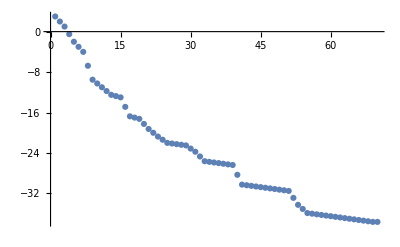

{1,3,15,6,69,-58,-9/2,-15/2,-6,-8,-117/4,-139/4,-57/4}

```mathematica
vals0={1,3,90}
meanmedmap=seqVals[vals0,10]
medsequence=seqmed[vals0,69]
ListPlot[{medsequence}]
```

```mathematica
firstmedseq=seqmed[vals0,151];
secmedseq=seqmed[vals0,152];
secmedseq=secmedseq[[2;;153]];   (*translate the second sequence over 1*)
secmedseq-firstmedseq
```

{-1.,-1.,-1.5,-1.5,-1.,-1.,-2.75,-2.75,-0.75,-0.75,-0.75,-0.75,-0.25,-0.25,-1.875,-1.875,-0.25,-0.25,-1.,-1.,-0.75,-0.75,-0.625,-0.625,-0.125,-0.125,-0.125,-0.125,-0.625,-0.625,-0.9375,-0.9375,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-1.9375,-1.9375,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-1.375,-1.375,-0.8125,-0.8125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,-0.125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

From this result, it is easy to see that our sequence of medians S_(n+1)-S_n≤ 0 ∀n∈ℕ  
This implies that the rate of change of S_n is always ≤ 0 and, as such, S_nis monotonically decreasing. Depending on the initial values chosen it can be either monotonically increasing or decreasing.

## Strong Terminating Conjecture Proof

This conjecture essentially says that for any set of real numbers S will converge to some number x_i. The conjecture states it as ∃k ϵ ℕ ∀j>k s.t. S_j=S_k We will start to prove this by defining a function that tracks the length of the sequence until a repeat is encountered. Now, ordinarily it might suffice to say that once S has a consecutive repeated value it will converge to that value immediately. This is not necessarily true, however, for the mean-median map. Within the paper, it is confirmed that any and all mean-median map sequences have two equal repeated values before converging and stabilizing. In fact, the unstable repeated values are equal to the stabilized final value. In the paper it is said that there has never been an example of convergence where this repetition doesn’t exist. Consequently, stating that one consecutive repeat of a value implies convergence is foolish.
	This can be avoided though due to the previous proof that the sequence of medians of the mean-median map is monotonic. If there were a point where the sequence of medians repeated itself, it would indicate that the change in median = 0. From our proof of the median sequence being monotonic, it becomes clear that the change in median cannot move above or below 0 once it reaches 0

```mathematica
numSteps[initSeq_]:=Module[
{numSteps=3,newSeq=seqVals[initSeq,3],initmedSeq=seqmed[initSeq,3],lastmed,currmed,currmedSeq},
(* Initialize these values *)
lastmed=initmedSeq[[-2]];
currmed=initmedSeq[[-1]];
currmedSeq=initmedSeq;
While[lastmed ≠  currmed,
(* promote lastVal and compute nextVal *)
lastmed=currmed;
currmed=N[Median[Append[newSeq,nextVal[newSeq]]]];
(*Append currVal to the currSeq*)
AppendTo[newSeq,nextVal[newSeq]];
AppendTo[currmedSeq,currmed];
numSteps++
];
numSteps
]
numSteps[vals0]
```

69

Here we input our starting sequence into numSteps and immediately we generate a small, equal number p of future iterations of the Mean-Median Map and of its Medians. This is so that we can pull up the second to last and last index of the sequence of medians. It should also be noted that this causes our numSteps (if starting at 0) to not count the p iterations done at initialization. Thus, we initialize numSteps at p=3.
Now, we will try the numSteps function on a variety of initial sequences!

```mathematica
vals[a_,b_]:={10,a,b};
Table[N[Mean[Table[numSteps[vals[a,b]],{a,1,50}]]],{b,1,50}]
```

{46.76,36.04,38.52,32.32,50.2,25.88,56.04,44.84,55.2,3.,54.12,42.48,49.52,23.4,51.24,28.48,30.28,38.32,43.56,30.96,45.52,38.08,59.72,42.88,31.72,46.76,46.92,29.,43.24,37.76,45.,49.4,51.12,47.08,67.64,56.6,46.04,63.28,80.56,34.6,62.12,52.12,57.24,61.6,48.36,39.52,60.76,82.04,71.72,49.8}

This output array shows the average number of steps needed for the median to converge for the first 50 values of a given some b from 1-50. The average step count was taken for simplicity’s sake. By taking the average for all values of a, it becomes clear that all values of a 1-50 for some b converge eventually (no errors in Mean[])!
Each value is this average for each value of b 1-50, so it implies that the medians converge for ALL values of a and for ALL values of b, at least with 1-50. 
This exploration leaves something to be desired in that this convergence has only been tested on an initial sequence of length 3. It appears, however, that it should still hold for any length of initial sequence! Simply adding in any new value into the sequence gives similar results. Due to limitations on computational power, we will not add a third parameter to iterate on and instead will allow reader-side input of other values.
On another note, it can be seen by expanding the limit on the value of a (0-20, 0-50, etc.) that the average for every b is consistently increasing. We will approach this next.

## Step Number is an Unbound Function

We will take a similar approach to the previous section to provide evidence for this conjecture. Verbatim, this paper stated “numerical investigations suggest that the number of steps needed until the
limiting median is attained is an unbounded function.”

Firstly, we will check if the number of steps until convergence is unbounded if a increases but b remains constant

657

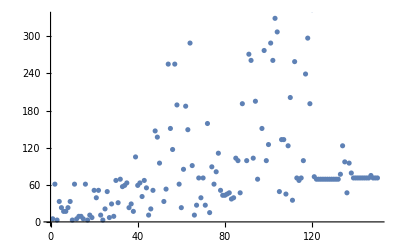

```mathematica
valbconst[a_]={10,a,3};
valconststep=Table[numSteps[valbconst[a]],{a,1,150}];
Max[valconststep]
ListPlot[valconststep]
```

Based on this graphical output, it would appear that at a certain point, the number of steps required for the medians to reach an equilibrium does level off! We can further prove this by comparing this maximum value with a higher a range.

```mathematica
valconststep=Table[numSteps[valbconst[a]],{a,1,150}];
Max[valconststep]
valconststep=Table[numSteps[valbconst[a]],{a,1,300}];
Max[valconststep]
```

657

657

Clearly, since the maxes did not change although the maximum a value changed implies that the numSteps function is bounded with just a as a variable. It remains to be seen, however, that it is bounded with inputs a AND b.

```mathematica
valab[a_,b_]={10,a,b};
valabstep=Table[Table[numSteps[valab[10*a,30*b]],{a,0,30}],{b,0,200}];
Max[valabstep]
ListPlot3D[valabstep]
```

3587

-Graphics3D-

```mathematica
Show[%661,ViewPoint->{0,0,∞}]
```

-Graphics3D-

Beautiful graphics, right? I love it. Anyway, as can be seen in the top-down viewpoint, there is a clear division  between the values for parameters a and b. As can be seen in the previous example, as parameter a increases, it eventually reaches a plateau. Once b is included into the mix, however, below a certain value, the medians do not converge so quickly. The maximum output for length that has been produced from this table of parameter values is 3587, but since there is no clear plateau for high a and low b values, it is unclear whether the medians will converge at some point. Unfortunately, as telling as these graphics may be, they also idicate that this dilemma cannot easily be given significant evidence using computers.

## Extra Conjectures!

51

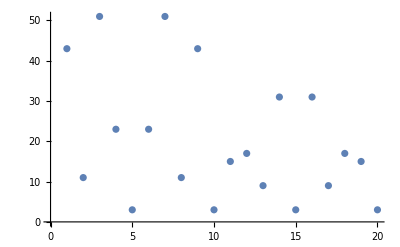

```mathematica
valus[a_,n_]={10,a,n};
n1=20;
n120=Table[numSteps[valus[a,n1]],{a,1,n1}];
Max[n120]
ListPlot[n120]
```

203

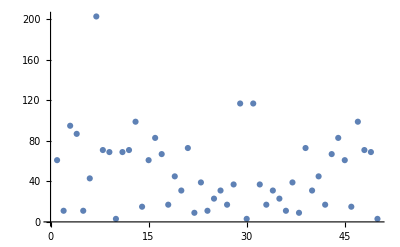

```mathematica
valus[a_,n_]={10,a,n};
n1=50;
n150=Table[numSteps[valus[a,n1]],{a,1,n1}];
Max[n150]
ListPlot[n150]
```

299

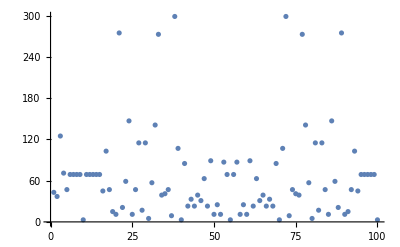

```mathematica
valus[a_,n_]={10,a,n};
n1=100;
n1100=Table[numSteps[valus[a,n1]],{a,1,n1}];
Max[n1100]
ListPlot[n1100]
```

After some preliminary experimentation, it becomes clear that a consistent pattern is formed when the third element in the array is = the limiting value of a. This calls for an expansion on this rule!

1445

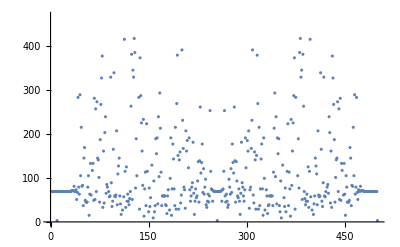

```mathematica
valus[a_,n_]={10,a,n};
n1=500;
n1500=Table[numSteps[valus[a,n1]],{a,1,n1}];
Max[n1500]
ListPlot[n1500]
```

```mathematica
valus[a_,n_]={10,a,n};
n1=1000;
Table[numSteps[valus[a,n1]],{a,1,n1}];
```

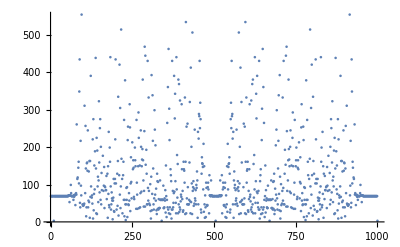

```mathematica
ListPlot[%]
```

Upon further investigations of these fractal patterns, it becomes clear that the apparent “center” of these fractals is actually 5 greater than what one would expect! One might expect the center of the fractal to be at exactly half of the selected n1 value. Furthermore, it can be observed graphically that the number of steps required for the median to converge actually increases at each increase in n1. This implies even more that it is potentially an unbounded function. 

Just Checking: Is this not amazing? I LOVE these beautifully ugly patterns and fractals! I love it even more that I can plot them AND make sense of them. I hope you enjoyed. Thanks!